## Lib + Model Inits

### FCM Lib Import

```mathematica
SetDirectory@NotebookDirectory[]
(*Needs["FCMLib`",FileNameJoin[{NotebookDirectory[],"FCMLib-cur.wl"}]]*)
Needs["FCMLib`",FileNameJoin[{"../lib","FCMLib-cur.wl"}]]
$FCMLibVersion

psotvs=Import["./psot-verts.csv", "CSV"];
psotvs⟦;;,2;;⟧=StringTrim/@psotvs⟦;;,2;;⟧; 

n = Length@psotvs

strongOrLink=$activationThreshold/2-0.001;orLink=strongOrLink-0.05;weakOrLink=$activationThreshold/4;
unsure=orLink;
andLink=$activationThreshold/4;
(* Strong vs Regular indicated by Fig 2.4; Specific to the al Qaeda case *)
(* Extra cross links informed by PD convos or by interpretation of PSOT papers *)

$stdActvnParams = {$activationFxn, $activationBias}
```

/Users/oosoba/Documents/RAND/Coding/fcm-fusion/fcm

Fuzzy Cognitive Map Library ver. 0.0.7+

34

{UnitStep,0.5}

### Model Specifications

#### PSOT v0

```mathematica
psotegsv0={
(* Original Tree structure *)
{1,6,strongOrLink},{2,6,strongOrLink},{3,6,strongOrLink},{4,6,orLink},{5,6,orLink},{30,6,weakOrLink},{31,6,weakOrLink},{32,6,weakOrLink},

{7,10,strongOrLink},{8,10,weakOrLink},{9,10,orLink},{24,10,strongOrLink},

{10,13,strongOrLink},{11,13,strongOrLink},{12,13,weakOrLink},

{14,18,strongOrLink (*unsure*)},{15,18,weakOrLink},{16,18,orLink},{17,18,orLink},

{19,23,strongOrLink (*unsure*)},{20,23,strongOrLink (*unsure*)},{21,23,-strongOrLink},{22,23,-strongOrLink},


(* Loose bits in orig factor tree *)
{25,11,orLink+0.1},(*fudge low fan-in nodes else never triggers*)
{24,7,strongOrLink+0.3},{24,11,strongOrLink},
{23,19,strongOrLink (*unsure*)},{23,20,strongOrLink (*unsure*)},{18,14,strongOrLink (*unsure*)},(*return links for uncertain causation*)


{6,50,andLink},{13,50,andLink},{18,50,andLink},{23,50,andLink} (*,TLD 'and' links*)
(*{50,50,orLink×orLink}, (* weak PSOT self-excitations for temporal correlation(?) *)*)


(*(* see pg 23 in PD+AOM2013 for next set of xlinks *)
{29,13,orLink},{29,21,-orLink},(* s/f links: Effects of successes ,{29,18,orLink} *)
{26,6,-orLink},{26,13,-orLink},(* Effects of Misbehaving grps {26,18,-orLink}, *)

{6,13,weakOrLink},{13,18,weakOrLink},{13,18,weakOrLink},{18,23, weakOrLink},(*rem l->r dep weak links*)
{6,29,weakOrLink} (* eff -> success *)*)
};

psotFCMv0 =FCM[psotvs,psotegsv0,0.7];
```

#### PSOT v2

```mathematica
psotegsv2={
(* Original Tree structure *)
{1,6,strongOrLink},{2,6,strongOrLink},{3,6,strongOrLink},{4,6,orLink},{5,6,orLink},{30,6,weakOrLink},{31,6,weakOrLink},{32,6,weakOrLink},

{7,10,strongOrLink},{8,10,weakOrLink},{9,10,orLink},{24,10,strongOrLink},

{10,13,strongOrLink},{11,13,strongOrLink},{12,13,weakOrLink},

{14,18,strongOrLink (*unsure*)},{15,18,weakOrLink},{16,18,orLink},{17,18,orLink},

{19,23,strongOrLink (*unsure*)},{20,23,strongOrLink (*unsure*)},{21,23,-strongOrLink},{22,23,-strongOrLink},


(* Loose bits in orig factor tree *)
{25,11,orLink+0.1},(*fudge low fan-in nodes else never triggers*)
{24,7,strongOrLink+0.3},{24,11,strongOrLink},
{23,19,strongOrLink (*unsure*)},{23,20,strongOrLink (*unsure*)},{18,14,strongOrLink (*unsure*)},(*return links for uncertain causation*)


{6,50,andLink},{13,50,andLink},{18,50,andLink},{23,50,andLink}, (*TLD 'and' links*)
{50,50,0.1}, (* weak PSOT self-excitations for temporal correlation(?) *)


(* see pg 23 in PD+AOM2013 for next set of xlinks *)
{29,13,orLink},{29,21,-(orLink+0.4)},(*succ links:Effects of successes*)
{6,29,weakOrLink},(*eff->success*)
{33,13,-orLink},{33,21,(orLink+0.4)},(*fail links:Effects of failures*)

{26,6,-strongOrLink},{26,13,-strongOrLink},(* Effects of Misbehaving grps {26,18,-orLink}, *)

{6,13,weakOrLink},{13,18,weakOrLink},{18,23, weakOrLink}(*rem l->r dep weak links*)
};
psotFCMv2 =FCM[psotvs,psotegsv2,0.7];
```

### Model Summaries

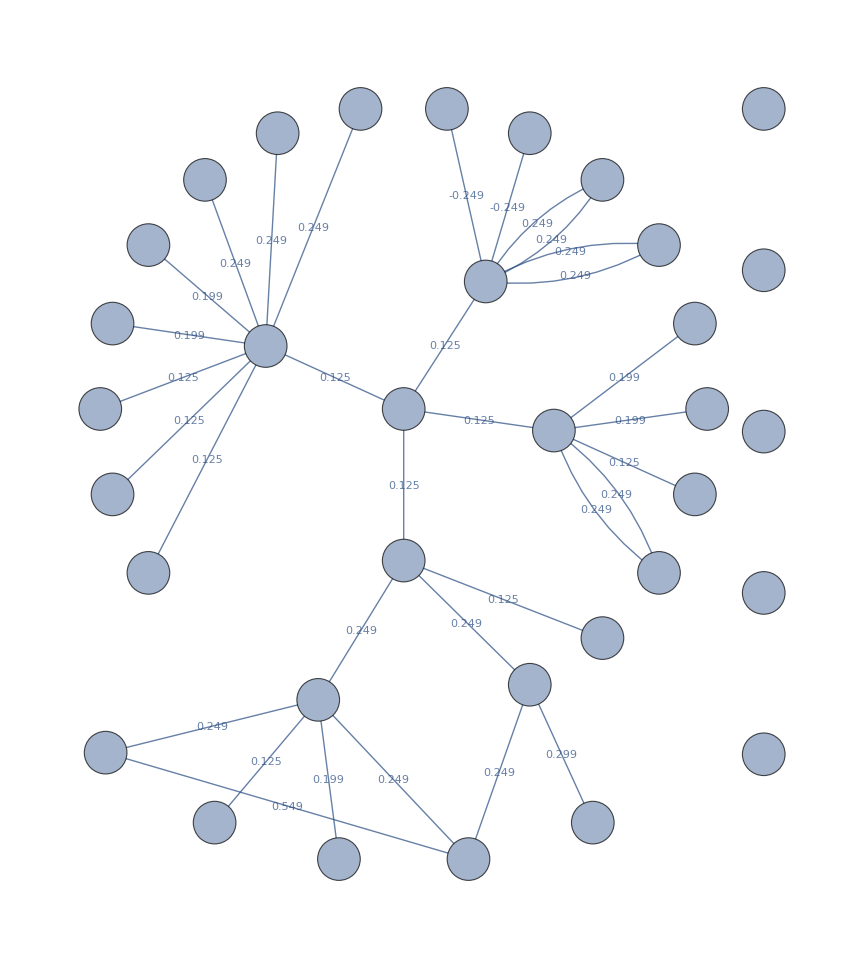

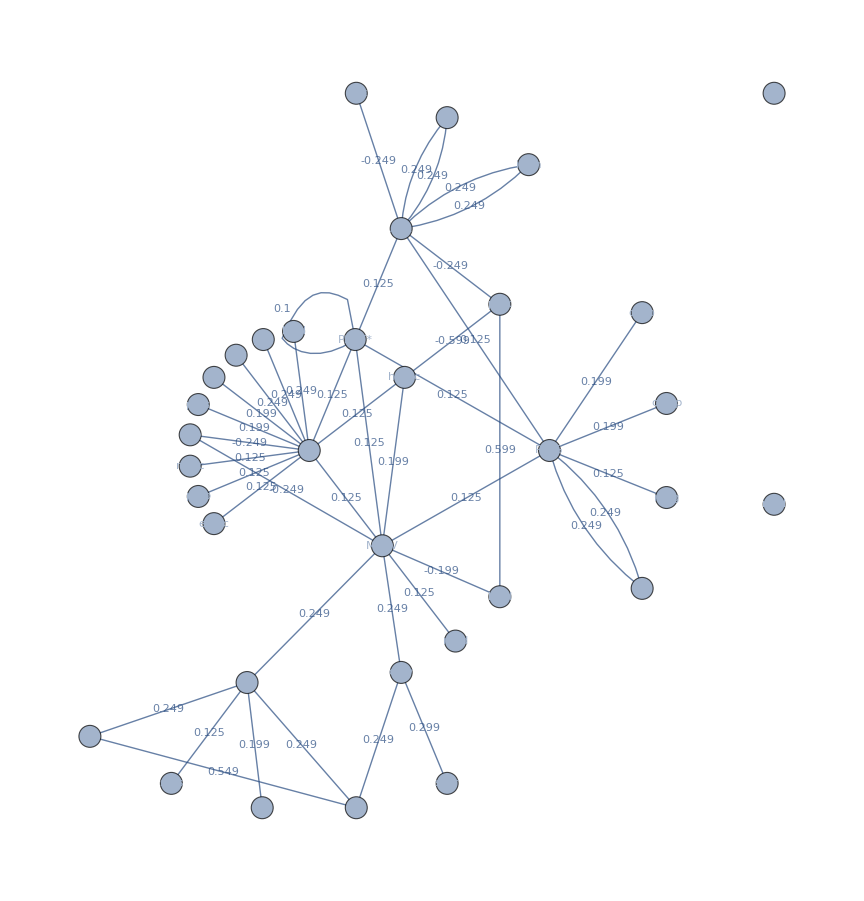

```mathematica
fcms = {psotFCMv0,psotFCMv1,psotFCMv2};

Graph[psotFCMv0,
GraphLayout->"RadialEmbedding",
ImageSize->72×12
]

(*Graph[psotFCMv1,
GraphLayout->"RadialEmbedding",
ImageSize->72×12
]*)

Graph[psotFCMv2,
GraphLayout->"RadialEmbedding",
ImageSize->72×12
]
```

## Illustrations

### Intro Predator-Prey Example

#### Specification

```mathematica
ppspec={
{1,2,1},{1,4,-1},
{2,3,1},{2,5,-1},
{3,2,-1},{3,5,-1},{3,4,1},
{4,1,1},{4,3,-1},{4,5,1},
{5,1,-1},{5,2,1},{5,4,-1}
};

ppvs={
{1,"C1","Herd Clustering"},
{2,"C2", "Fatigue"},
{3,"C3", "Rest"},
{4,"C4", "Survival Threat"},
{5,"C5","Run Away"}
};
ppvs={
{1,"C1: Herd\nClustering"},
{2,"C2: Fatigue"},
{3,"C3: Rest"},
{4,"C4: Survival\nThreat"},
{5,"C5: Run Away"}
};
ppvs⟦;;,2⟧ = Map[Style[#, 22,Bold]&, ppvs⟦;;,2⟧]
```

{C1: Herd
Clustering,C2: Fatigue,C3: Rest,C4: Survival
Threat,C5: Run Away}

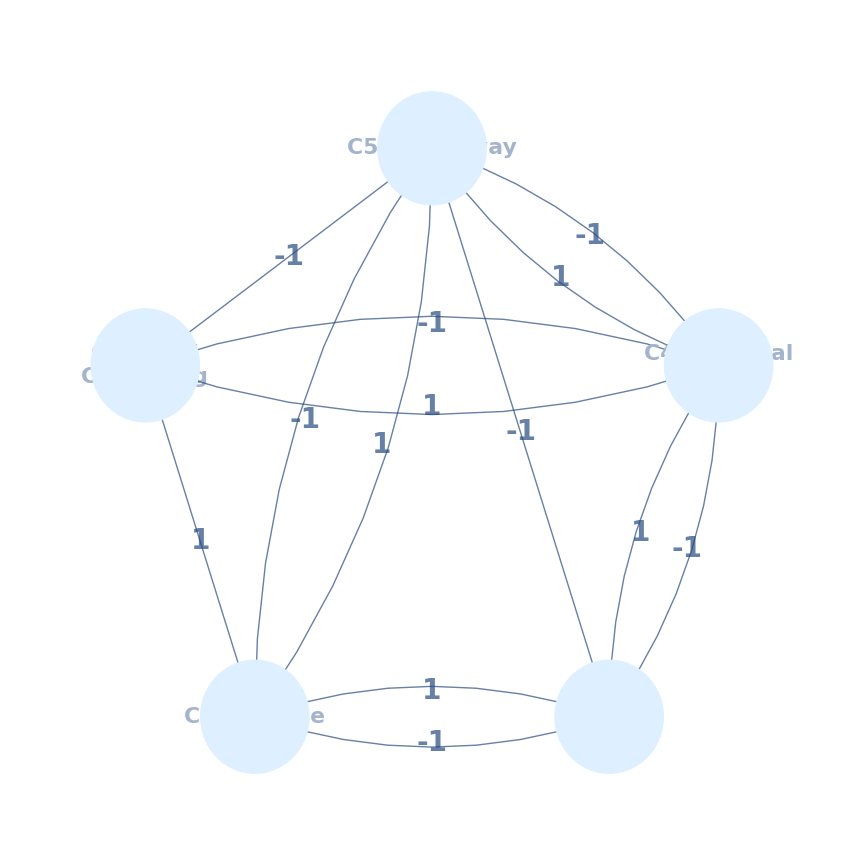

herd-dyn.eps

```mathematica
ppFCM =FCM[ppvs,ppspec,0.375];

Graph[
ppFCM,
GraphLayout->"CircularEmbedding",
EdgeLabelStyle->Directive[28, Bold],
EdgeStyle->Thick,
EdgeShapeFunction->GraphElementData[{"CarvedArrow","ArrowSize"->0.03}],
VertexLabels->PropertyValue[ppFCM, VertexLabels],
VertexShape->Graphics[{EdgeForm[Thick],LightBlue,Disk[{0,0},0.5×{1.5,1}]}],
ImageSize->72×12
]

Export["herd-dyn.eps", %, "EPS"]
```

### FCM - PSOT Graphs

```mathematica
sz=12;
Grid[{{
Graph[psotFCMv0,
GraphLayout->"BalloonEmbedding",
VertexLabelStyle->Directive[FontFamily->"Arial", 20, Bold],
EdgeStyle->Directive[Hue[0.625, 0.5, 0.7],Arrowheads[{{.2,.1}}]],
ImageSize->72×sz
],
Graph[FCM[psotvs,psotegsv2],
VertexShapeFunction->"Square",
VertexSize->{.25,.12}, 
VertexStyle->LightRed(* Hue[0.125,0.7,0.9]*),
VertexLabelStyle->Directive[FontFamily->"Arial", 20, Bold],
EdgeStyle->Directive[Hue[0.625, 0.5, 0.7],Arrowheads[{{.2,.1}}]],
(*GraphLayout->{"VertexLayout"->"LayeredDigraphEmbedding", "EdgeLayout"->"DividedEdgeBundling", "PackingLayout"-> "NestedGrid"},(*"RadialEmbedding",*)*)
ImageSize->72×sz(*,GraphStyle->"DiagramGold"*)
]
}},
Frame->All
]
```

```mathematica
{{-Graphics-, -Graphics-}}
```

```mathematica
Export["model-comp.pdf",{{-Graphics-, -Graphics-}}]
```

model-comp.pdf

```mathematica
sz=12;
Grid[{{
Graph[psotFCMv0,
GraphLayout->"BalloonEmbedding",
VertexLabelStyle->Directive[FontFamily->"Arial", 20, Bold],
(*EdgeStyle->Directive[Hue[0.625, 0.5, 0.7],Arrowheads[{{.2,.1}}]],*)
ImageSize->72×sz,
GraphStyle->"DiagramGold"
],
Graph[FCM[psotvs,psotegsv2],(*VertexShapeFunction->"Square",VertexStyle->LightRed Hue[0.125,0.7,0.9],*)
VertexSize->{.25,.12}, 
GraphLayout->"SpringElectricalEmbedding",
VertexLabelStyle->Directive[FontFamily->"Arial", 20, Bold],
(*EdgeStyle->Directive[Hue[0.625, 0.5, 0.7],Arrowheads[{{.2,.1}}]],*)
ImageSize->72×sz,
GraphStyle->"DiagramGold"
]
}},
Frame->All
]

Export["model-comp.eps", %, "EPS"]
```

-Graphics- | -Graphics-

model-comp.eps

```mathematica
msz = 10;
GraphicsRow[
{
MatrixPlot[
FCMat@psotFCMv0, 
ImageSize->msz×72,
ImageMargins->0,Mesh->All,
Frame->True,
FrameTicks->{None,None},
PlotLegends->Automatic,
PlotLabel->Style["Original", 22, Bold]
],
MatrixPlot[
FCMat@psotFCMv2, 
ImageSize->msz×72(*Large*),
ImageMargins->0,Mesh->All,
Frame->True,
FrameTicks->{None,None},
PlotLegends->Automatic,
PlotLabel->Style["Dynamic", 22, Bold]
]},
ImageMargins->0,
ImageSize->72×msz×2.3,
Spacings->1,
PlotLabel->Style["Matrix Intensity Plot of FCM-PSOT Connection Matrices", 32, Bold]
]

Export["fcm-psot-dbl.eps",%,"EPS"]
```

-Graphics-

```mathematica
Export["/Users/oosoba/Documents/RAND/Coding/fcm-fusion/fcm/fcm-psot-dbl.eps",%105,"EPS"]
```

/Users/oosoba/Documents/RAND/Coding/fcm-fusion/fcm/fcm-psot-dbl.eps

### Activation Functions

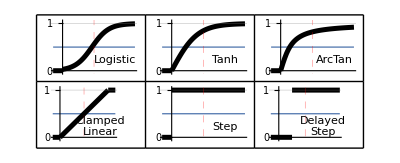

```mathematica
th=0;
fgs = {
Max[0,LogisticSigmoid[7.5t-3.5]]×UnitStep[t],
Max[0,Tanh[2.5t ]],
Max[0,2 ArcTan[7t]/π],
Min[1,Max[0,t-th]],
UnitStep[t-th],
UnitStep[t-0.25]
};
lbls={"Logistic", "Tanh", "ArcTan", "Clamped\nLinear", "Step", "Delayed\nStep"};

GraphicsGrid[
Partition[
Table[
Plot[
{0.5,fgs⟦pt⟧},
{t,-0.15,1.15},
(*PlotLegends->"Expressions",*)
GridLines->{{{0.5,Directive[Red, Thick, Dashed]}}, {0,1}},
ImageSize->72×5,
Axes->{False,True},
Ticks->{None,{0, 0.5,1}},
PlotRange->{{-0.15,1.15}, {-0.05, 1.05}},
PlotStyle->{Thick,Directive[Black,Thickness[0.01]]},
Epilog->Inset[Text[Style[lbls⟦pt⟧, 14, Bold]],Scaled[{0.75,0.26}]]
],
{pt,6}
],3],
ImageSize->Full,
Frame-> All
]
(*Export["/Users/oosoba/Documents/RAND/a.Running Projects/Writing Projects/FCM for Fusion [JDMS]/jdms-latex/actvn-fxns.pdf",%219,"PDF"]*)

Export["actvn-fxns.eps",%, "EPS"]
```

```mathematica
Export["/Users/oosoba/Documents/RAND/Coding/fcm-fusion/fcm/actvn-fxns.eps",%15,"EPS"]
```

/Users/oosoba/Documents/RAND/Coding/fcm-fusion/fcm/actvn-fxns.eps

```mathematica
NotebookDirectory[]
```

/Users/oosoba/Documents/RAND/Coding/fcm-fusion/fcm/

### FCM Combination Demo

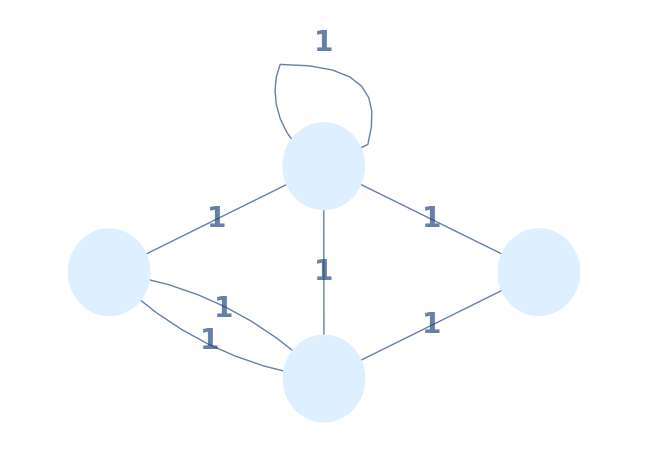
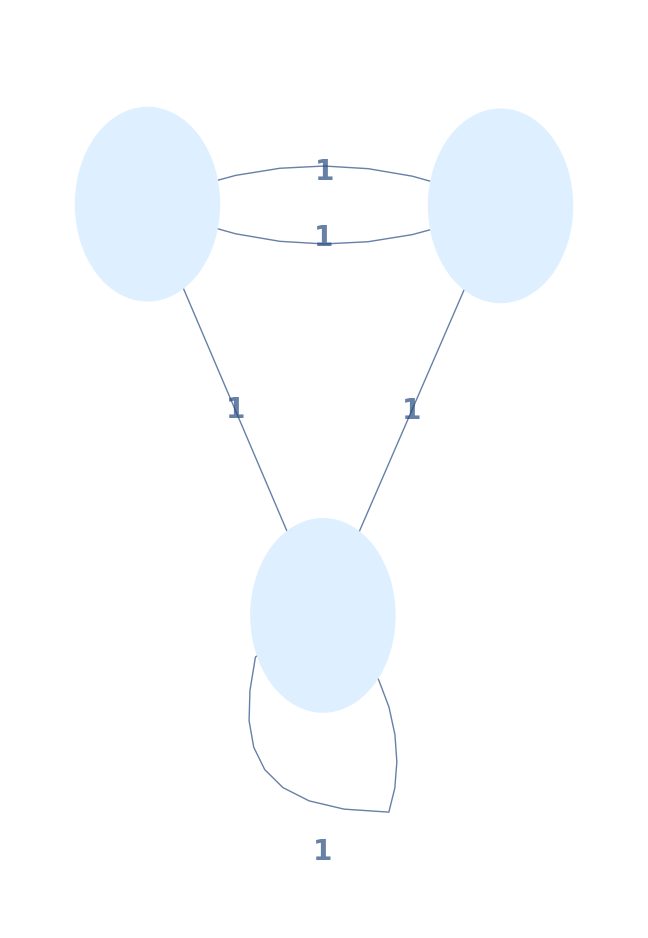
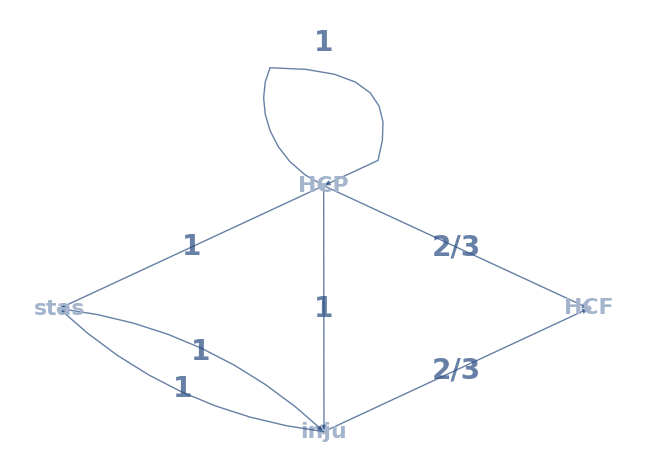
-Graphics- | -Graphics- | -Graphics-
(1 | 1 | 1 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 1
0 | 0 | 0 | 0) | (1 | 1 | 1
0 | 0 | 1
0 | 1 | 0) | (1 | 1 | 1 | 2/3
0 | 0 | 1 | 0
0 | 1 | 0 | 2/3
0 | 0 | 0 | 0)

fcm-combo.eps

```mathematica
nds = {
{1,"HCP","Hypercoagulation Positional Factors"},
{2,"stas", "Blood Stasis"},
{3,"inju", "Endothelial Injury"},
{4,"HCF", "Hypercoagulation Factors"}
};
nds⟦;;,2⟧ = Map[Style[#, 22,Bold]&, nds⟦;;,2⟧];
(*gspec={{1,2,1},{1,3,-1},{1,4,1},{2,4,-1},{3,1,-1},{3,4,-1},{3,2,1},{4,3,1}};
altGspec={{1,2,1},{1,4,1},{2,4,1},{3,1,-1},{3,2,1},{4,3,1}};

gspec={{1,1,1},{1,2,0.4},{1,3,1}, {1,4,1},{2,3,0.5},{3,2,0.4},{3,4,0.75}};
altGspec={{1,1,1},{1,2,0.4},{1,3,1},{2,3,0.5},{3,2,0.4}};*)

gspec={{1,1,1},{1,2,1},{1,3,1}, {1,4,1},{2,3,1},{3,2,1},{3,4,1}};
altGspec={{1,1,1},{1,2,1},{1,3,1},{2,3,1},{3,2,1}};


expFCMs = {FCM[nds,gspec,0.5],FCM[nds⟦;;3⟧,altGspec,0.5]};
combFCM =FCMJoin[nds,expFCMs,{2,1}];
compfcms = Flatten@{expFCMs, combFCM};


compfcms=Table[
Graph[
f,
(*GraphLayout->"StarEmbedding",*)
EdgeLabelStyle->Directive[28, Bold],
EdgeStyle->Thick,
EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->0.073}],
VertexLabels-> (PropertyValue[f, VertexLabels]),
VertexShape->Graphics[{EdgeForm[Thick],LightBlue,Disk[{0,0},0.5×{1.5,1}]}],
ImageSize->72×9
], {f, compfcms}
];

Grid[
{
compfcms,
Panel/@(Style[#,22]&/@((MatrixForm@FCMat[#])&/@compfcms))
},
(*ImageSize->72×16,*)
Spacings->{0,0}
]
(*Export["fcm-combo.pdf",%]*)
(*Export["fcm-combo.eps",%]*)
```

## Differential Hebbian Learning Exploration

0.34375

0.19875

0.580879

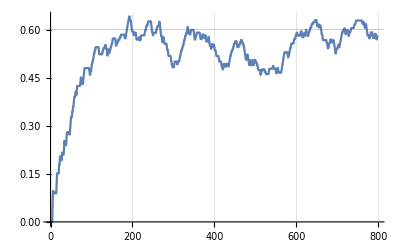

```mathematica
ns = 800;
e01True = 0.6;
C0 = UnitStep[
RandomVariate[BernoulliDistribution[0.35], ns]-0.1
];

(*e21True = -0.95; C2 = UnitStep[RandomVariate[BernoulliDistribution[0.2], ns]-0.1];*)
(*C1 = UnitStep[e01True×C0 (*+ e21True×C2*)-0.1];*)
(*C1 = UnitStep[e01True×C0 -0.1];*)
C1 = UnitStep[
Table[RandomVariate[BernoulliDistribution[e01True×p]],{p,C0}]-0.1
];

(*ListPlot[{C0,C1}(*, Joined->True*)]*)
N@Mean@C0
N@Mean@C1
ecur = 0;
dhl=Flatten@Last@Reap@Do[
μ =0.1/Log[1+t]; (*0.1(1-t/(1.1×ns));*)(* 0.1/Log[1+t];*)
ΔC0=C0⟦t⟧-C0⟦t-1⟧;
ΔC1=C1⟦t⟧-C1⟦t-1⟧;
enext = If[ΔC0==0,
ecur,
ecur+ μ(ΔC0×ΔC1-ecur)
];
Sow@enext;
ecur = enext;
,{t, 2, ns-1}
];

Mean@dhl⟦-25;;⟧
ListLinePlot[
dhl,
GridLines->{Automatic,{{e01True,Red}}}
]
```

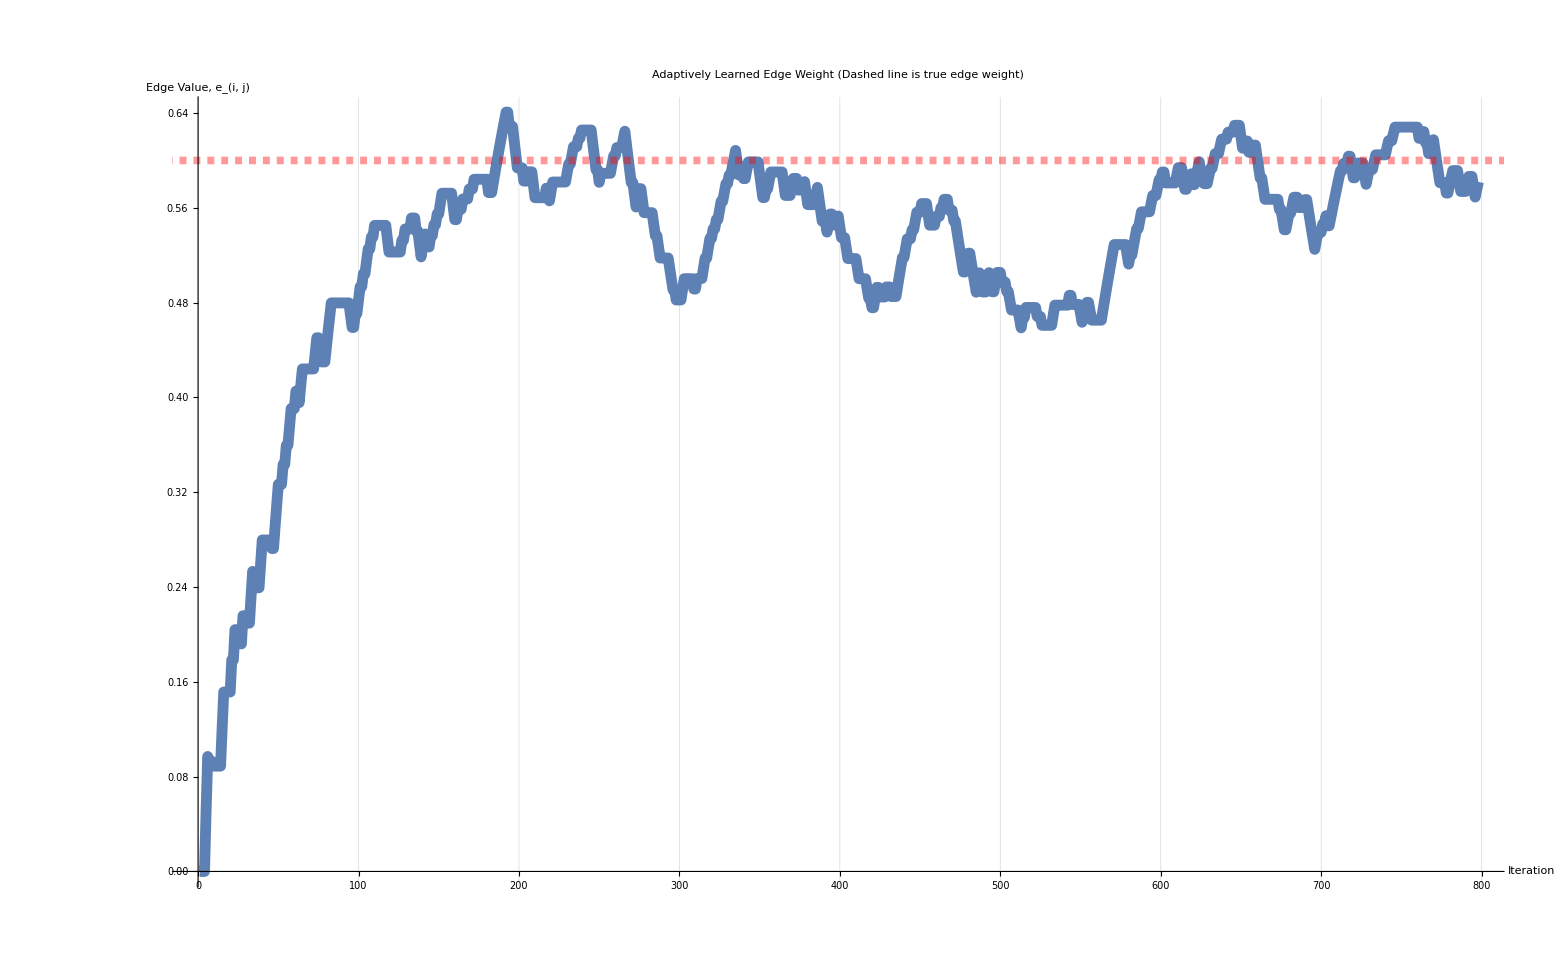

fcm-edge-adapt.eps

```mathematica
ListLinePlot[
dhl,
GridLines->{Automatic,{{e01True,Directive[Red, Thickness[0.0035], Dashed]}}},
PlotStyle->Thickness[0.005],
AxesLabel->(Style[#,24,Bold]&/@{"Iteration","Edge\nValue, e_(i, j)"}),
TicksStyle->Directive[Bold, 22],
ImageSize->72×24,
PlotLabel->Style["Adaptively Learned Edge Weight\n(Dashed line is true edge weight)",26,Bold],
Epilog->Inset[
Graph[
{1,2},{1->2},(*{"lvic"->"ACR"},*)
VertexSize->0.2,
EdgeLabels->{1->2->Placed["e_(i, j)",1/2]},
EdgeLabelStyle->Directive[32, Bold],
EdgeStyle->Thick,
EdgeShapeFunction->GraphElementData[{"FilledArrow","ArrowSize"->0.073}],
VertexLabels->{
1->Placed[Style["lvic",28,Bold],Center],
2->Placed[Style["ACR",28,Bold],Center]
},
(*VertexShape->Graphics[{EdgeForm[Thick],LightBlue,Disk[{0,0},0.5×{1.5,1}]}],*)
ImageSize->72×9
],
Scaled[{0.65,0.2}]
]
]
(*Export["/Users/oosoba/Documents/RAND/a.Running Projects/Writing Projects/FCM for Fusion [JDMS]/jdms-latex/fcm-edge-adapt.pdf",%132,"PDF"]*)
Export["fcm-edge-adapt.eps",%,"EPS"]
```

## Unused

### Taber’s Platelet Aggregation Example

#### Specification

```mathematica
clotspec={
{1,1,1},
{1,2,0.4},
{1,3,1}, (* edge mising from adj mat in paper *)
{1,4,1},
{2,3,0.5},
{2,6,0.45},
{3,2,0.4},
{3,4,0.75},
{3,6,0.4},
{4,6,0.4},
{5,6,0.45},
{6,2,0.7},
{7,5,-0.6},
{8,6,0.95},
{9,10,-0.9},
{10,6,1},
{11,8,0.95},
{12,11,-0.6}
};(* from Taber et al on quantization effects in FCMs *)

clotvs={
{1,"HCP","Hypercoagulation Positional Factors"},
{2,"stas", "Blood Stasis"},
{3,"inju", "Endothelial Injury"},
{4,"HCF", "Hypercoagulation Factors"},
{5,"ADP","Adenosine Diphosphate"},
{6,"PAgg", "Platelet Aggregation"},
{7,"clop", "Clopidogrel Ticlopidogrel"},
{8,"A2", "Thromboxane A2"},
{9,"war","Warfarin"},
{10,"K", "Vitamin K Activated Clotting Factors"},
{11,"cox", "Cyclooxidase COX-1"},
{12,"aspi", "Aspirin"}
};
```

```mathematica
(*psotFCMv0 =FCM[psotvs,psotegsv0,0.7];*)
clotFCM =FCM[clotvs,clotspec,0.25];

Show[
Graph[clotFCM,
GraphLayout->"RadialEmbedding",
ImageSize->72×12
],
Framed->True
]
```

```mathematica
Map[Style[#,18]&,clotvs⟦;;,;;⟧,{2}]
```

```mathematica
Head@First@%
```

```mathematica
Length[%62]
```

```mathematica
Framed@Row[{
TableForm[
Map[Style[#,14]&,clotvs⟦;;,;;⟧,{2}],
TableAlignments->{Center, Right,Left}, 
TableSpacing->{2,1.5},
TableHeadings->{None,Style[#,18,Bold]&/@{"", "Label", "Description"}}
],
"|",

Show[
Graph[clotFCM,
GraphLayout->"RadialEmbedding",
ImageSize->72×10
]
]
},
ImageSize->72×16
]
```

```mathematica
Export["fcm-sample.png", %]
```